### Solve differential equations of population growth

#### Set constants

```mathematica
ClearAll[S0,R0,K,S,R,s,r,t,α,μ1,μ2]
S0=1*^2;
R0=1*^2;
P0=1*^5;
K=1*^3;
d=0.3;
tmax=105;
```

#### Population growth equations - simple

```mathematica
(*solution = DSolve[{
S'[t]==μ1*S[t]-α*S[t],
R'[t]==μ2*R[t]+α*S[t]
},{S[t],R[t]},t];*)
```

#### Population growth equations - logistic growth

```mathematica
solution = ParametricNDSolve[{
S'[t]==μ1*(1-((S[t]+R[t])/K))*S[t]-α*S[t],
R'[t]==μ2*(1-((S[t]+R[t])/K))*R[t]+α*S[t]-d*R[t],
WhenEvent[S[t]==1,S[t]->0],
S[0]==S0,R[0]==R0},
{S,R},
{t,0,tmax},
{μ1,μ2,α}]
```

{S→ParametricFunction[<>],R→ParametricFunction[<>]}

```mathematica
(*solution = ParametricNDSolve[{
S'[t]==μ1*(1-((S[t]+R[t])/K))*S[t]-α*(P[t]/P0)*S[t],
R'[t]==μ2*(1-((S[t]+R[t])/K))*R[t]+α*(P[t]/P0)*S[t]-d*R[t],
P'[t]==α*P[t],
WhenEvent[S[t]==1,S[t]->0],
S[0]==S0,R[0]==R0,P[0]==P0},
{S,R,P},
{t,0,tmax},
{μ1,μ2,α}]*)
```

{S→ParametricFunction[<>],R→ParametricFunction[<>],P→ParametricFunction[<>]}

#### Assign equations to functions

```mathematica
s[t_]=S[t]/.solution
r[t_]=R[t]/.solution
```

ParametricFunction[<>][t]

ParametricFunction[<>][t]

#### Plot

```mathematica
mu1={.8};
(*mu2={.75,.78};*)
mu2={.775}
alp={.1};
plotmax=10;

params=Join@@@Table[{m1/m2,α},{m1,mu1},{α,alp},{m2,mu2}];
```

{0.775}

```mathematica
{0.775}
```

```mathematica
DensityPlot[Log10[S[.8,.75,α][t]]/.solution,{t,0,100},{α,.1,.3}]
```

$Aborted

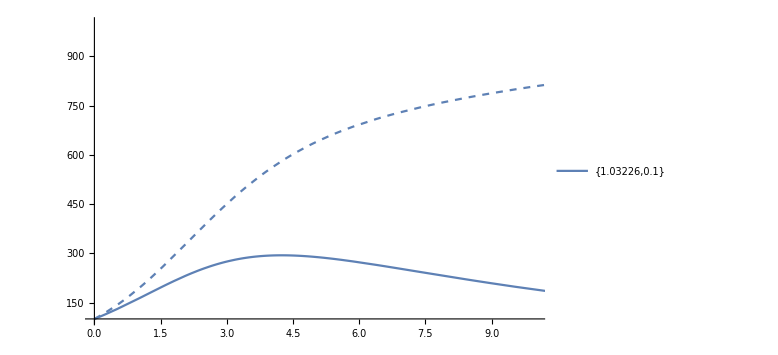

```mathematica
Show[Plot[
Evaluate@Table[S[μ1,μ2,α][t]/.solution,
{μ1,mu1},{α,alp},{μ2,mu2}],
{t,0,tmax},
PlotStyle->Thick,
PlotLegends->{params},
PlotRange->{{0,plotmax},{100,1000}}
],
Plot[
Evaluate@Table[R[μ1,μ2,α][t]/.solution,
{μ1,mu1},{α,alp},{μ2,mu2}],
{t,0,tmax},
PlotStyle->Dashed,
PlotRange->All],
Plot[5,{t,0,plotmax},PlotStyle->Red],
ImageSize->Large]
```

```mathematica
(*Show[Plot[Evaluate@Table[{
Log[s[t,.8,μ2,α]],
Log[r[t,.8,μ2,α]]},
{μ2,{.75,.78}},{α,{.1,.3}}],
{t,1,20},
PlotLegends->{"S","R"},
AxesLabel->{{"t"},"Population"},
PlotStyle->Thick],ImageSize->Large]*)
```